# AntonAntonov/CallGraph

Call graph generation

## Paclet Manifest

"Documentation"

"English"

"Guides"

"Callgraphscreation.nb"DocumentationEnglishGuidesCallgraphscreation.nb

"ReferencePages"

"Symbols"

"CallGraphAddPrintDefinitionsButtons.nb"DocumentationEnglishReferencePagesSymbolsCallGraphAddPrintDefinitionsButtons.nb

"CallGraphAddUsageMessages.nb"DocumentationEnglishReferencePagesSymbolsCallGraphAddUsageMessages.nb

"CallGraphBiColorCircularEmbedding.nb"DocumentationEnglishReferencePagesSymbolsCallGraphBiColorCircularEmbedding.nb

"CallGraph.nb"DocumentationEnglishReferencePagesSymbolsCallGraph.nb

"FunctionDependencies.nb"DocumentationEnglishReferencePagesSymbolsFunctionDependencies.nb

"NodeInducedEdges.nb"DocumentationEnglishReferencePagesSymbolsNodeInducedEdges.nb

"NodeInducedInEdges.nb"DocumentationEnglishReferencePagesSymbolsNodeInducedInEdges.nb

"NodeInducedOutEdges.nb"DocumentationEnglishReferencePagesSymbolsNodeInducedOutEdges.nb

"Tutorials"

"Kernel"

"CallGraph.wl"KernelCallGraph.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

A paragraph that describes your paclet in more detail.

### Details

This package provides functions for making a call graph between the functions that belong to specified contexts.

The main function CallGraph gives a graph with vertices that are functions names and edges that show
which functions call which other functions.

With the default option values the graph vertices are labeled and have tooltips with function usage messages.

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`CallGraph`"];
```

### Basic Examples

Get a paclet:

```mathematica
PacletInstall["AntonAntonov/SSparseMatrix"];
Needs["AntonAntonov`SSparseMatrix`"];
```

Generate a call graph with usage tooltips:

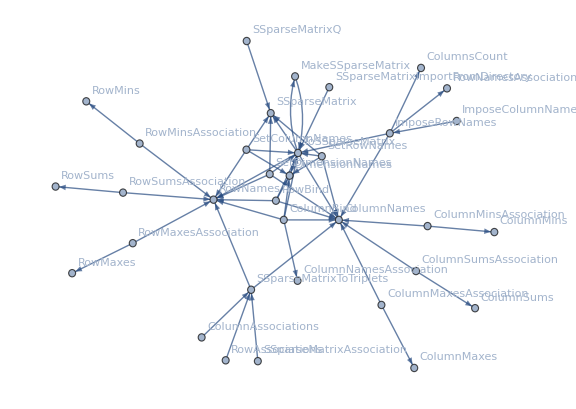

```mathematica
CallGraph["AntonAntonov`SSparseMatrix`",ImageSize->Large]
```

### Scope

Generate a call graph with exclusions:

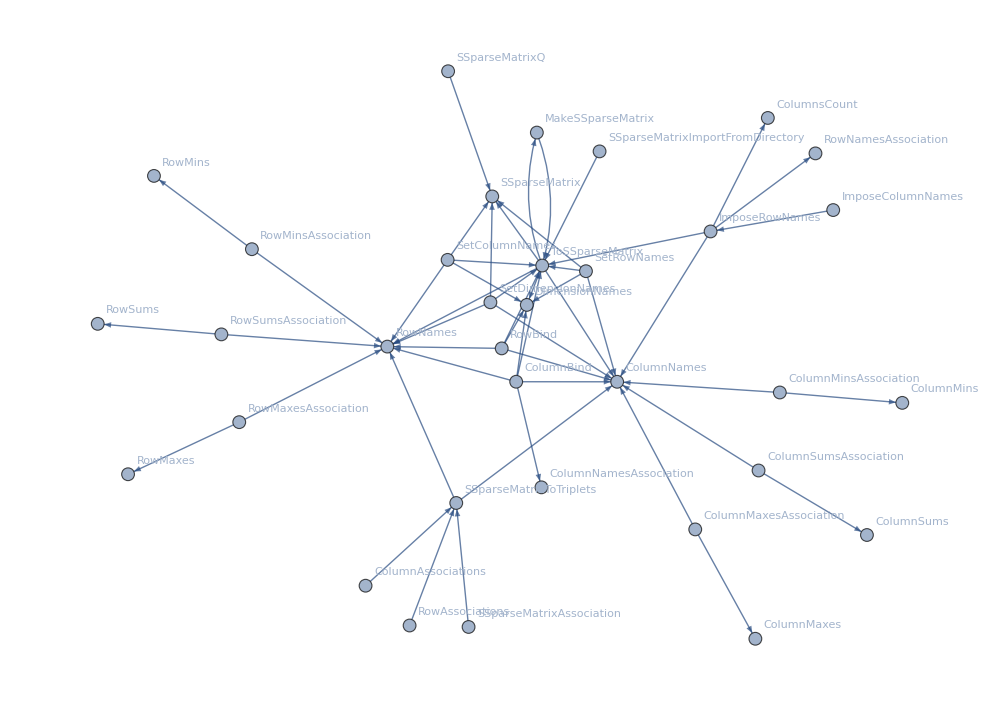

```mathematica
CallGraph["AntonAntonov`SSparseMatrix`",Exclusions->{$TrieRoot,$TrieValue},ImageSize->1000]
```

Generate call graph with buttons to print definitions:

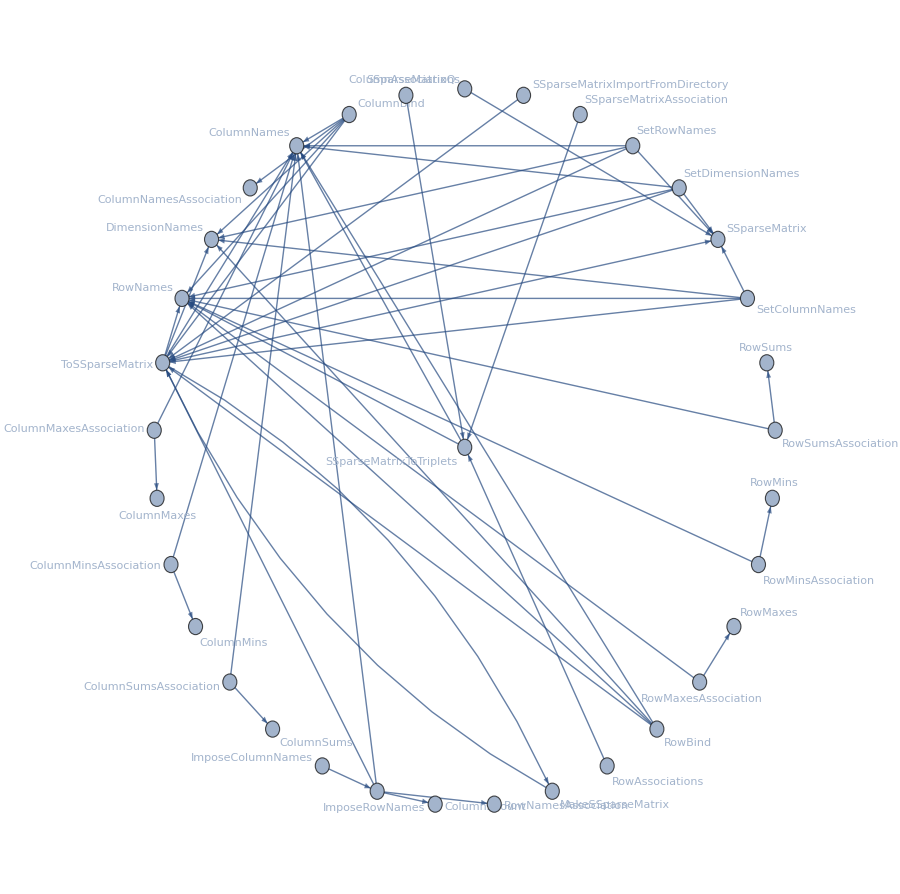

```mathematica
gr0=CallGraph["AntonAntonov`SSparseMatrix`","UsageTooltips"->False];
gr1=CallGraphAddPrintDefinitionsButtons[gr0,GraphLayout->"StarEmbedding",ImageSize->900]
```

Generate circular embedding graph edge coloring:

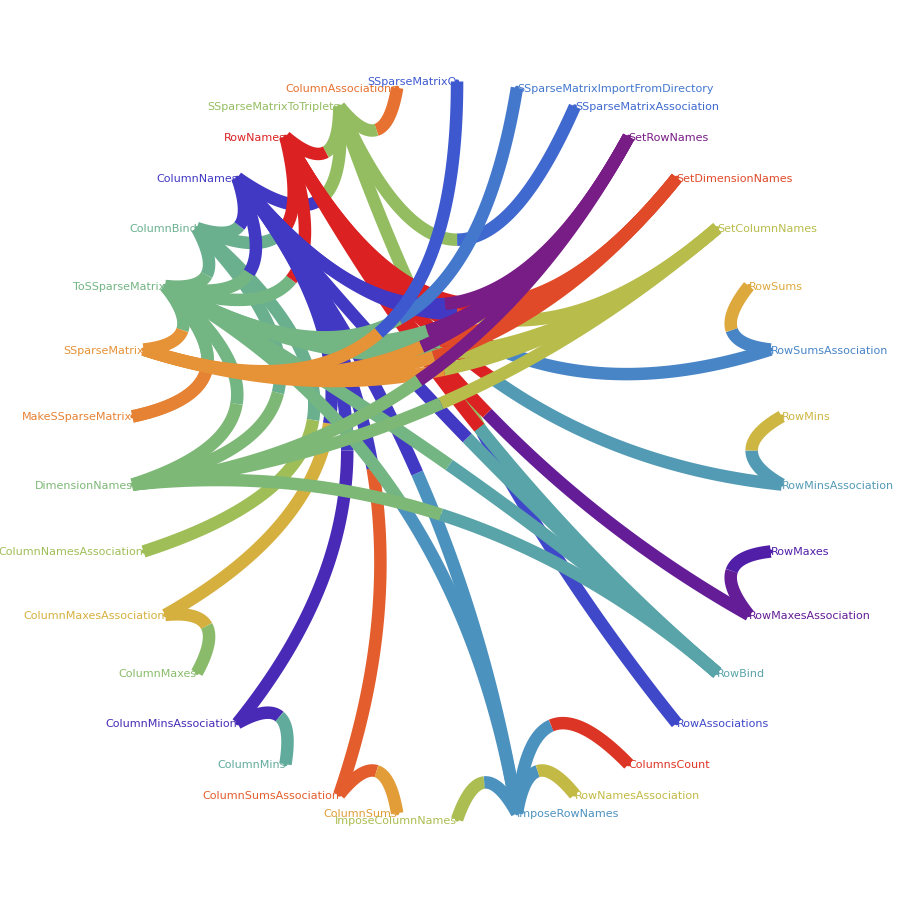

```mathematica
SeedRandom[33];
cols=RandomSample[ColorData["Rainbow"]/@Rescale[Range[VertexCount[gr1]]]];
CallGraphBiColorCircularEmbedding[gr1,"VertexColors"->cols,ImageSize->900,PlotTheme->"Web"]
```

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-CallGraph-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Call graph

Dependencies

Down values

Sub values

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

AntonAntonov/SSparseMatrix

### Original Source References and Attributions

Call graph generation for context functions | Mathematica for prediction algorithms

### Links

MathematicaForPrediction/CallGraph.m at master · antononcube/MathematicaForPrediction · GitHub

### Compatibility

#### Wolfram Language Version

12.1+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.